Program calculating bound states for dipole-dipole interaction for a given short-range phase
Everything in units of R_d and E_d (characteristic length and energy for dipole-dipole interaction)

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\Oem\Desktop\Dipoles final

Parameters:
β = (R_v/R_d)^4
Lmax - maximal value of angular momentum L
xi - minimal value of r in the grid
xf -maximal value of r in the grid
nptl - number of points to tabulate the wavelenght
npt - numeber of point per de Broglie wavelenght in the grid 
emin - mimimal energy for bound state searching
emax - maximal energy for bound state searching
epsf - small number used to determine final point of integration
nptf - number of points to tabulate the final point of integration

```mathematica
Lmax=32;xi=0.2;xf=100;Id=IdentityMatrix[Lmax/2+1];nptl=200;npt=20;epsf=10^-3;epsi=10^-3;nptf=50;dxf=10;
freq=30000; 
freqz=0.1 freq;
d=10/(137*2);
m = 9.18 BohrM;
BohrM = 1.3996 (*MHz/Gauss*)
dp=0.2;
phimin =- N[π/2-0.01];
phimax=N[π/2-0.01];
```

1.3996

Conversion factor from Hz to Eh

```mathematica
HztoEh=1.519829 10^(-16);
```

Debye  in atomic units

```mathematica
Debye=0.393456;
```

Mass unit  in atomic units

```mathematica
massunit=1.661 10^(-24)/(9.110 10^(-28)); (*Unit/Masa elektronu*)
```

Parameters for Dy atoms

```mathematica
μ=81.25 massunit; (*Masa zredukowana*)
```

```mathematica
C6=2277;
```

```mathematica
Dperm=0.22 Debye;
```

Trap frequency and harm. osc. length

```mathematica
ω=2 π freq HztoEh; ωz=2 π freqz HztoEh;aHO=(1/Sqrt[μ ω])/R6; aHOz=(1/Sqrt[μ ωz])/R6
(*ωz=2 π freqz HztoEh;aHOz=(1/Sqrt[μ ωz])/R6*)
```

1535.02/R6

van der Waals length and energy

```mathematica
R6=(2 μ C6)^(1/4)
E6=1/(2 μ R6^2)
```

161.164

1.29946×10^-10

Characteristic length and energy for dipole-dipole interaction (vdw units)

```mathematica
C3=2d^2;R3=2 μ C3/R6;E3=(1/(2μ (R6 R3)^2))/E6;
β=R3
R3
```

4.89741

4.89741

Harmonic oscillator energy in vdW units

```mathematica
α=(1/aHO)^4
αz=(1/aHOz)^4;
```

0.0121509

```mathematica
Ω=2 Sqrt[α];
Ωz=2 Sqrt[αz]
```

0.0220462

```mathematica
α=(Ω/2)^2;
αz=(Ωz/2)^2
```

0.000121509

Energy scale

```mathematica
emin=-0.001 Ωz ;emax=-20 Ωz;
```

Mean scattering length of vdW potential

```mathematica
abar=2 Pi/Gamma[1/4]^2;abar1=Gamma[1/4]^6/(144 Pi^2 Gamma[3/4]^2)abar ;aHO/abar
```

6.3013

Spherical Bessel functions

```mathematica
jl[l_,x_]:=Sqrt[Pi/(2x)]BesselJ[l+1/2,x];nl[l_,x_]:=(-1)^(l+1) Sqrt[Pi/(2x)]BesselJ[-l-1/2,x]
```

Potentials

```mathematica
Vho[l1_,ml1_,l2_,ml2_]:= (If[l1==l2,1,0]If[ml1==ml2,1,0]-(1-αz/α)If[ml1==ml2,1,0]/3((-1)^ml1 Sqrt[2 l1 +1]Sqrt[2l2 +1] 2 ThreeJSymbol[{l1,0},{2,0},{l2,0}]ThreeJSymbol[{l1,-ml1},{2,0},{l2,ml2}] + If[l1==l2,1,0]));
Vedd[l1_,ml1_,l2_,ml2_]:=-(-1)^ml1 Sqrt[2 l1 +1]Sqrt[2l2 +1]  ThreeJSymbol[{l1,0},{2,0},{l2,0}]ThreeJSymbol[{l1,-ml1},{2,0},{l2,ml2}];(*Dodać symbol wignera*)
Vmdd[l1_,ml1_,l2_,ml2_]:=-(-1)^ml1 Sqrt[2 l1 +1]Sqrt[2l2 +1]  ThreeJSymbol[{l1,0},{2,0},{l2,0}]ThreeJSymbol[{l1,-ml1},{2,0},{l2,ml2}];
Vvdw[l1_,ml1_,l2_,ml2_]:= -If[l1==l2,1,0]If[ml1==ml2,1,0];
```

```mathematica
Veddtab=Developer`ToPackedArray[N[Table[Vedd[l1,0,l2,0],{l1,0,Lmax,2},{l2,0,Lmax,2}]]];
Vmddtab=Developer`ToPackedArray[N[Table[Vmdd[l1,0,l2,0],{l1,0,Lmax,2},{l2,0,Lmax,2}]]];
Vvdwtab=Developer`ToPackedArray[N[Table[Vvdw[l1,0,l2,0],{l1,0,Lmax,2},{l2,0,Lmax,2}]]];
Vhotab=Developer`ToPackedArray[N[Table[Vho[l1,0,l2,0],{l1,0,Lmax,2},{l2,0,Lmax,2}]]];
Vcftab = Developer`ToPackedArray[N[Table[If[l1==l2,l1(l1+1),0],{l1,0,Lmax,2},{l2,0,Lmax,2}]]];
Veddtab2=Developer`ToPackedArray[N[Table[Vedd[l1,0,l2,0],{l1,1,Lmax,2},{l2,1,Lmax,2}]]];
Vmddtab2=Developer`ToPackedArray[N[Table[Vmdd[l1,0,l2,0],{l1,1,Lmax,2},{l2,1,Lmax,2}]]];
Vvdwtab2=Developer`ToPackedArray[N[Table[Vvdw[l1,0,l2,0],{l1,1,Lmax,2},{l2,1,Lmax,2}]]];
Vhotab2=Developer`ToPackedArray[N[Table[Vho[l1,0,l2,0],{l1,1,Lmax,2},{l2,1,Lmax,2}]]];
Vcftab2 = Developer`ToPackedArray[N[Table[If[l1==l2,l1(l1+1),0],{l1,1,Lmax,2},{l2,1,Lmax,2}]]];
```

ClebschGordan::tri: ThreeJSymbol[{0,0},{2,0},{0,0}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{0,0},{2,0},{4,0}] is not triangular.

General::stop: Further output of ClebschGordan::tri will be suppressed during this calculation.

ClebschGordan::tri: ThreeJSymbol[{0,0},{2,0},{0,0}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{0,0},{2,0},{4,0}] is not triangular.

General::stop: Further output of ClebschGordan::tri will be suppressed during this calculation.

ClebschGordan::tri: ThreeJSymbol[{0,0},{2,0},{0,0}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{0,0},{2,0},{4,0}] is not triangular.

General::stop: Further output of ClebschGordan::tri will be suppressed during this calculation.

ClebschGordan::tri: ThreeJSymbol[{1,0},{2,0},{5,0}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{1,0},{2,0},{7,0}] is not triangular.

General::stop: Further output of ClebschGordan::tri will be suppressed during this calculation.

ClebschGordan::tri: ThreeJSymbol[{1,0},{2,0},{5,0}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{1,0},{2,0},{7,0}] is not triangular.

General::stop: Further output of ClebschGordan::tri will be suppressed during this calculation.

ClebschGordan::tri: ThreeJSymbol[{1,0},{2,0},{5,0}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{1,0},{2,0},{7,0}] is not triangular.

General::stop: Further output of ClebschGordan::tri will be suppressed during this calculation.

```mathematica
Vhotable[x_]:=N[(Table[Vhotab[[l1/2+1,l2/2+1]],{l1,0,Lmax,2},{l2,0,Lmax,2}])/.{r->x}];
Veddtable[x_]:=N[(Table[Veddtab[[l1/2+1,l2/2+1]],{l1,0,Lmax,2},{l2,0,Lmax,2}])/.{r->x}];
```

```mathematica
1/α Vhotable[1]//MatrixForm
1/β Veddtable[1]//MatrixForm
```

(55.1399 | -24.2913 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
-24.2913 | 39.6208 | -20.8211 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | -20.8211 | 41.0316 | -20.5429 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | -20.5429 | 41.3138 | -20.461 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | -20.461 | 41.4178 | -20.4259 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | -20.4259 | 41.4675 | -20.4077 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | -20.4077 | 41.4951 | -20.3969 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | -20.3969 | 41.512 | -20.3901 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | -20.3901 | 41.5231 | -20.3855 | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -20.3855 | 41.5308 | -20.3823 | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -20.3823 | 41.5364 | -20.3799 | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -20.3799 | 41.5405 | -20.3781 | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -20.3781 | 41.5437 | -20.3767 | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -20.3767 | 41.5462 | -20.3756 | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -20.3756 | 41.5481 | -20.3747 | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -20.3747 | 41.5497 | -20.374
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -20.374 | 41.551)

(0. | -0.0913163 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
-0.0913163 | -0.0583399 | -0.0782711 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | -0.0782711 | -0.0530362 | -0.0772254 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | -0.0772254 | -0.0519755 | -0.0769175 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | -0.0769175 | -0.0515847 | -0.0767855 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | -0.0767855 | -0.0513978 | -0.0767169 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | -0.0767169 | -0.051294 | -0.0766767 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | -0.0766767 | -0.0512303 | -0.0766511 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.0766511 | -0.0511885 | -0.0766338 | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.0766338 | -0.0511596 | -0.0766215 | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.0766215 | -0.0511387 | -0.0766126 | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.0766126 | -0.0511232 | -0.0766058 | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.0766058 | -0.0511113 | -0.0766005 | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.0766005 | -0.051102 | -0.0765964 | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.0765964 | -0.0510946 | -0.0765931 | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.0765931 | -0.0510886 | -0.0765904
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.0765904 | -0.0510837)

Matrix containg potential

```mathematica
V[r_]:=1/r^2 Vcftab + 1/r^6 Vvdwtab +β/r^3 Veddtab+α r^2 Vhotab;
V2[r_]:=1/r^2 Vcftab2 + 1/r^6 Vvdwtab2 +β/r^3 Veddtab2+α r^2 Vhotab2;
```

```mathematica
V[1]//MatrixForm
Id//MatrixForm
ref =0*Table[Sort[Eigenvalues[V[10]]][[1]],{n,1,Lmax/2+1}]
refdiag = 0*DiagonalMatrix[ref]//MatrixForm
```

(-0.991859 | -2.19378 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
-2.19378 | 3.60659 | -1.88038 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | -1.88038 | 17.734 | -1.85526 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | -1.85526 | 39.7595 | -1.84786 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | -1.84786 | 69.7689 | -1.84469 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | -1.84469 | 107.773 | -1.84304 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | -1.84304 | 153.776 | -1.84207 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | -1.84207 | 207.777 | -1.84146 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | -1.84146 | 269.778 | -1.84104 | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -1.84104 | 339.779 | -1.84075 | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -1.84075 | 417.78 | -1.84053 | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -1.84053 | 503.78 | -1.84037 | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -1.84037 | 597.78 | -1.84024 | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -1.84024 | 699.78 | -1.84015 | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -1.84015 | 809.781 | -1.84007 | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -1.84007 | 927.781 | -1.84
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -1.84 | 1053.78)

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

(0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.)

Short range solution for van der Waals potential, with the short range phase "phi"

```mathematica
sol0[l_,r_,phi_]=Sin[phi] Sqrt[r]BesselJ[1/4,1/(2 r^2)]+Cos[phi]Sqrt[r] BesselY[1/4,1/(2 r^2)];(*nie ma l*)
```

Table of short range solutions

```mathematica
Psi0[r_,ph_]:=Table[If[l1==l2,sol0[l1,r,ph],0] ,{l1,0,Lmax,2},{l2,0,Lmax,2}]
```

Adiabatic potentials (diagonalized V[r]) + van der Waals potential

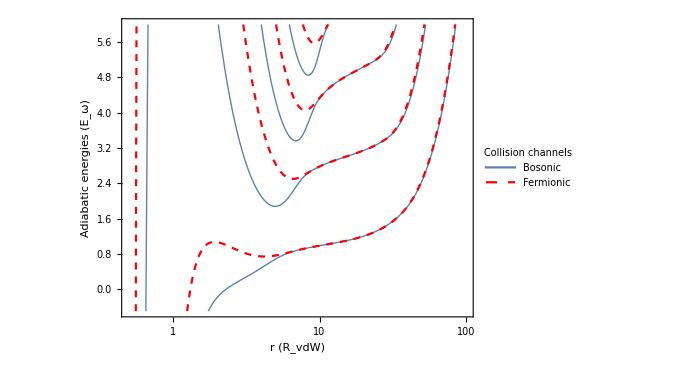

```mathematica
LogLinearPlot[{1/Ω(Take[Sort[Eigenvalues[V[x]]],Lmax/2+1]-ref),1/Ω(Take[Sort[Eigenvalues[V2[x]]],Lmax/2]-Take[ref,Lmax/2])},{x,0.5,xf},
PlotRange->{-0.5,6},AxesOrigin->{0.5,0},
AspectRatio->0.75,
Frame->True, FrameStyle->{{Directive[Thickness[0.005],Black],Directive[Thickness[0.005],Black]},{Directive[Thickness[0.005],Black],Directive[Thickness[0.005],Black]}},
PlotStyle->{Thick,{Red,Dashed}},PlotLegends->Placed[LineLegend[{Style["Bosonic",FontFamily->"Times",FontWeight->Bold],Style["Fermionic",FontFamily->"Times",FontWeight->Bold]}, LegendLabel->Style["Collision channels",FontSize->14, FontFamily->"Times",FontWeight->Bold],LegendFunction->(Framed[#,RoundingRadius->0,Background->White]&),LegendMargins->5],{Left,Top}],FrameLabel->{Style["r (R_vdW)",FontSize->20, FontFamily->"Times New Roman",FontWeight->Bold],Style["Adiabatic energies (E_ω)",FontSize->20,FontWeight->Bold, FontFamily->"Times"]},GridLines->Automatic, GridLinesStyle->Directive[Thin, Dashed, LightGray],ImagePadding->50,ImageSize->500]
```

Subroutine determining final point of integration versus energy. This speeds up the numerical calculations. The plot shows final point of integration versus Log[10,-E]

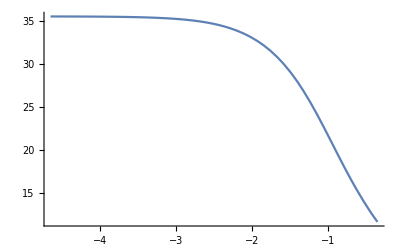

```mathematica
Module[{pemin,pemax,dp,TurnPoint,k,ExpInt,p,x,tabf},TurnPoint[e_?NumericQ]:=x/.FindRoot[e+1/x^6-αz x^2==0,{x,xi,xf}][[1]];(*Przybliżenie WKB*)
k[x_,e_]:=Sqrt[-(e+1/x^6-αz x^2)];
ExpInt[rf_?NumericQ,e_?NumericQ]:=NIntegrate[k[x,e],{x,TurnPoint[e],rf}];
pemin=Log[10,-emin];
pemax=Log[10,-emax];
tabf=Table[{p,x/.FindRoot[Exp[-ExpInt[x,-10^p]]==epsf,{x,TurnPoint[-10^p],xf}][[1]]},{p,pemin,pemax,(pemax-pemin)/nptf}];xfin=Interpolation[tabf];
Plot[xfin[x],{x,pemin,pemax}]]
```

Subroutine determining steps
Parameters:
npt -  number of points per one wave-lenght

InterpolatingFunction::dmval: Input value {0.100039} lies outside the range of data in the interpolating function. Extrapolation will be used.

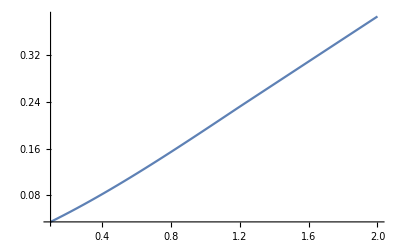

```mathematica
Module[{tab,eig,lambda,h,dbl,n},

tab=Table[eig=Eigenvalues[V[x]];{x,Min[Flatten[{2Pi/Sqrt[Abs[emin-eig]],2Pi/Sqrt[Abs[emax-eig]]}]]},{x,xi,xf,(xf-xi)/nptl}];
lambda=Interpolation[tab]; (*Local de Broglie wavelength (minimum over all channels). Used for determination of the step size *)

xt={};
h=lambda[xi]/npt;
AppendTo[xt,xi];
AppendTo[xt,xi+h];
dbl=1; (* dbl = 1 - step doubling or halving was done in the previous step, dbl = 0 otherwise *)
n=2;

While[(xt[[n]]<xf)||(dbl==1),
Which[
(lambda[xt[[n]]]≥2 npt h)&&(dbl==0),

h=2h;
AppendTo[xt,xt[[n]]+h];
dbl=1;,

(lambda[xt[[n]]]<npt h)&&(dbl==0),

h=h/2;
AppendTo[xt,xt[[n]]+h];
dbl=1;,

True,

AppendTo[xt,xt[[n]]+h];
dbl=0;
];
n++;
];
nstep=n;  (* Total number of steps *);
Plot[lambda[x],{x,0.1,2},PlotRange->All]
]
```

Number of steps

```mathematica
nstep
```

3230

Matching point (somewhere between xi and xf in the classically allowed regime). It position is determined versus position of the classical turning point for highest L

```mathematica
xmid=(x/.FindRoot[Sort[Eigenvalues[V[x]]][[1]]-ref[[1]]==emax,{x,xi,xf}][[1]])
```

1.33945

Location of the matching point in the table xt

```mathematica
nmid=1; 
While[xt[[nmid]]<xmid,nmid++];
nmid--
xt[[nmid]]
```

260

1.33146

Subroutine performing outward integration using renormalized Numerov method
It takes Psi0 as an initial condition

Parameters:
en - energy
n0 -  starting point (element of xt)
nf -  final point (element of xt)
phi - short-range phase
cl: if 1 clears table Rout (to save memory)

```mathematica
evolNumOut[en_?NumericQ,n0_?IntegerQ,nf_?IntegerQ,phi_?NumericQ,cl_?IntegerQ]:=
Module[{W,Qt,n,Rinv,h,h0,nodes,Ro},

nodes=0;

Rout[n0]=Psi0[xt[[n0+1]],phi].Inverse[Psi0[xt[[n0]],phi]];
nodes+=Length[Select[Eigenvalues[Rout[n0]],#<0&]];(*Which functions change sign*)
h=xt[[n0+1]]-xt[[n0]];
n=n0+1;

While[n<=nf,
h0=h;
h=xt[[n+1]]-xt[[n]];
Which[

Abs[h]>1.5 Abs[h0],
W=Id+(h^2/12) QT[[n+1]];
Rout[n]=Inverse[W].(2 Id -(5h^2/6)QT[[n]]-(Id+(h^2/12)QT[[n-2]]).Inverse[Rout[n-1].Rout[n-2]]);,

Abs[h]<0.75 Abs[h0],
Qt=(en + ref[[1]])Id-V[(xt[[n]]+xt[[n-1]])/2];
Rinv=Inverse[2 Id-(h0^2/12)Qt].((Id+(h0^2/12)QT[[n-1]]).Inverse[Rout[n-1]]+Id+(h0^2/12)QT[[n]]);
W=Id+(h^2/12) QT[[n+1]];
Rout[n]=Inverse[W].((2 Id -(5h^2/6)QT[[n]])-(Id+(h^2/12)Qt).Rinv);,

True,
W=Id+(h^2/12) QT[[n+1]];
Rout[n]=Inverse[W].((2 Id -(5h^2/6)QT[[n]])-(Id+(h^2/12)QT[[n-1]]).Inverse[Rout[n-1]]);
];
nodes+=Length[Select[Eigenvalues[Rout[n]],#<0&]];
n++;
];
Ro=Rout[nf];
Clear[W,Qt,n,Rinv,h,h0];
If[cl==1,Clear[Rout]];
{Ro,nodes}]
```

Subroutine performing inward integration using renormalized Noumerov method
It assumes that function vanishes at the starting value

Parameters:
Parameters:
en - energy
n0 -  starting point (element of xt)
nf -  final point (element of xt)
cl: if 1 clears table Rout (to save memory)

```mathematica
evolNumIn[en_?NumericQ,n0_?IntegerQ,nf_?IntegerQ,cl_?IntegerQ]:=
Module[{W,Qt,n,Rinv,h,h0,nodes,Ri},

nodes=0;
h=xt[[n0-2]]-xt[[n0-1]];
W=Id+(h^2/12) QT[[n0-2]];
Rin[n0-1]=Inverse[W].(2 Id -(5h^2/6)QT[[n0-1]]);
nodes+=Length[Select[Eigenvalues[Rin[n0-1]],#<0&]];
n=n0-2;

While[n>=nf,
h0=h;
h=xt[[n-1]]-xt[[n]];
Which[

Abs[h]>1.5 Abs[h0],
W=Id+(h^2/12) QT[[n-1]];
Rin[n]=Inverse[W].(2 Id -(5h^2/6)QT[[n]]-(Id+(h^2/12)QT[[n+2]]).Inverse[Rin[n+1].Rin[n+2]]);,

Abs[h]<0.75 Abs[h0],
Qt=(en+ref[[1]]) Id-V[(xt[[n]]+xt[[n+1]])/2];
Rinv=Inverse[2 Id-(h0^2/12)Qt].((Id+(h0^2/12)QT[[n+1]]).Inverse[Rin[n+1]]+Id+(h0^2/12)QT[[n]]);
W=Id+(h^2/12) QT[[n-1]];
Rin[n]=Inverse[W].((2 Id -(5h^2/6)QT[[n]])-(Id+(h^2/12)Qt).Rinv);,

True,
W=Id+(h^2/12) QT[[n-1]];
Rin[n]=Inverse[W].((2 Id -(5h^2/6)QT[[n]])-(Id+(h^2/12)QT[[n+1]]).Inverse[Rin[n+1]]);
];
nodes+=Length[Select[Eigenvalues[Rin[n]],#<0&]];
n--;
];
Ri=Rin[nf];
Clear[W,Qt,n,Rinv,h,h0];
If[cl==1,Clear[Rin]];
{Ri,nodes}]
```

Subroutine calculating determinant that should vanish at the matching point if the energy is correct

Parameters:
en -  energy
phi -  short range phase

```mathematica
EigenEn[en_?NumericQ,phi_?NumericQ]:=
Module[{n,win,wout,nodes,det,m,nmax},
QT=Table[(en+ref[[1]]) Id-V[xt[[n]]],{n,1,Length[xt]}];
nmax=nstep;
While[xt[[nmax]]>xfin[Log[10,-en]],nmax--];
win=evolNumIn[en,nmax,nmid+1,1]; (* Performs inward integration *)
wout=evolNumOut[en,1,nmid,phi,1];  (* Performs outward integration *)
nodes=win[[2]]+wout[[2]]; (* Total number of nodes *) 
m=wout[[1]]-Inverse[win[[1]]];
det=Det[m]; (*Calculates determinant that should vanish at the the matching point *)
Clear[n,win,wout,QT];
{det,nodes,m}
]
```

```mathematica
Timing[EigenEn[-3.,Pi/4]]
```

InterpolatingFunction::dmval: Input value {0.477121} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{0.21875,{1.23177×10^-12,19,{{0.0376085,-0.00213321,0.000247367,0.0000195642,6.93146×10^-7,1.46715×10^-8,2.08182×10^-10,2.12177×10^-12,1.62892×10^-14,9.75779×10^-17,4.68722×10^-19,1.84534×10^-21,6.06181×10^-24,1.68648×10^-26,4.02451×10^-29,8.32749×10^-32,1.50829×10^-34},{-0.00213315,0.0483459,-0.00266181,-0.0000364149,-5.95543×10^-7,-7.99086×10^-9,-8.43303×10^-11,-7.04576×10^-13,-4.73811×10^-15,-2.60899×10^-17,-1.19461×10^-19,-4.60934×10^-22,-1.5159×10^-24,-4.29169×10^-27,-1.05511×10^-29,-2.27023×10^-32,-4.30523×10^-35},{0.000247398,-0.00266182,0.0736739,-0.00181473,-0.0000130861,-1.26267×10^-7,-1.08095×10^-9,-7.65472×10^-12,-4.4199×10^-14,-2.08558×10^-16,-8.10472×10^-19,-2.61738×10^-21,-7.08358×10^-24,-1.61726×10^-26,-3.1272×10^-29,-5.1197×10^-32,-7.04131×10^-35},{0.0000195679,-0.0000364161,-0.00181474,0.10178,-0.00135174,-5.76988×10^-6,-3.5224×10^-8,-2.02099×10^-10,-1.01269×10^-12,-4.34732×10^-15,-1.59399×10^-17,-5.00773×10^-20,-1.35587×10^-22,-3.18564×10^-25,-6.5416×10^-28,-1.18229×10^-30,-1.89332×10^-33},{6.9334×10^-7,-5.956×10^-7,-0.0000130865,-0.00135174,0.130662,-0.00107744,-3.06304×10^-6,-1.3078×10^-8,-5.43263×10^-11,-2.03042×10^-13,-6.67449×10^-16,-1.91795×10^-18,-4.81863×10^-21,-1.06165×10^-23,-2.06011×10^-26,-3.53832×10^-29,-5.4067×10^-32},{1.46772×10^-8,-7.99234×10^-9,-1.26279×10^-7,-5.77001×10^-6,-0.00107744,0.159953,-0.000895497,-1.81819×10^-6,-5.76731×10^-9,-1.82787×10^-11,-5.33062×10^-14,-1.39448×10^-16,-3.24555×10^-19,-6.70947×10^-22,-1.23359×10^-24,-2.02264×10^-27,-2.96781×10^-30},{2.08291×10^-10,-8.43559×10^-11,-1.08114×10^-9,-3.52265×10^-8,-3.0631×10^-6,-0.0008955,0.189488,-0.00076618,-1.16562×10^-6,-2.86188×10^-9,-7.17033×10^-12,-1.68278×10^-14,-3.59786×10^-17,-6.93939×10^-20,-1.20386×10^-22,-1.8787×10^-25,-2.64163×10^-28},{2.12319×10^-12,-7.04893×10^-13,-7.65694×10^-12,-2.0213×10^-10,-1.30787×10^-8,-1.81822×10^-6,-0.000766182,0.219189,-0.000669689,-7.90945×10^-7,-1.54975×10^-9,-3.15189×10^-12,-6.09306×10^-15,-1.08677×10^-17,-1.76853×10^-20,-2.61539×10^-23,-3.51217×10^-26},{1.63027×10^-14,-4.74107×10^-15,-4.4217×10^-14,-1.01295×10^-12,-5.43333×10^-11,-5.7676×10^-9,-1.16563×10^-6,-0.000669691,0.249019,-0.000595023,-5.6071×10^-7,-8.979×10^-10,-1.51349×10^-12,-2.45483×10^-15,-3.71304×10^-18,-5.17296×10^-21,-6.60613×10^-24},{9.76765×10^-17,-2.61115×10^-17,-2.08669×10^-16,-4.34903×10^-15,-2.03088×10^-13,-1.82808×10^-11,-2.86201×10^-9,-7.90955×10^-7,-0.000595025,0.278958,-0.000535591,-4.11545×10^-7,-5.49077×10^-10,-7.80067×10^-13,-1.07765×10^-15,-1.40104×10^-18,-1.69144×10^-21},{4.69286×10^-19,-1.19588×10^-19,-8.11007×10^-19,-1.59485×10^-17,-6.67681×10^-16,-5.33169×10^-14,-7.17104×10^-12,-1.54982×10^-9,-5.60717×10^-7,-0.000535592,0.308997,-0.000487204,-3.10716×10^-7,-3.50919×10^-10,-4.26103×10^-13,-5.07692×10^-16,-5.73797×10^-19},{1.84794×10^-21,-4.61542×10^-22,-2.61942×10^-21,-5.01127×10^-20,-1.91889×10^-18,-1.39492×10^-16,-1.68308×10^-14,-3.15218×10^-12,-8.97935×10^-10,-4.11551×10^-7,-0.000487205,0.339133,-0.000447077,-2.40146×10^-7,-2.32679×10^-10,-2.4434×10^-13,-2.53768×10^-16},{6.07174×10^-24,-1.51833×10^-24,-7.08983×10^-24,-1.35707×10^-22,-4.82177×10^-21,-3.24702×10^-19,-3.5989×10^-17,-6.09407×10^-15,-1.51361×10^-12,-5.49097×10^-10,-3.1072×10^-7,-0.000447079,0.369365,-0.000413289,-1.89298×10^-7,-1.59159×10^-10,-1.46011×10^-13},{1.68965×10^-26,-4.29986×10^-27,-1.61881×10^-26,-3.18909×10^-25,-1.06252×10^-23,-6.71355×10^-22,-6.94229×10^-20,-1.08706×10^-17,-2.45521×10^-15,-7.80128×10^-13,-3.50931×10^-10,-2.40149×10^-7,-0.00041329,0.399696,-0.000384468,-1.51744×10^-7,-1.11816×10^-10},{4.03308×10^-29,-1.05746×10^-29,-3.13026×10^-29,-6.55005×10^-28,-2.0622×10^-26,-1.23455×10^-24,-1.20455×10^-22,-1.76922×10^-20,-3.71396×10^-18,-1.0778×10^-15,-4.26135×10^-13,-2.32686×10^-10,-1.893×10^-7,-0.00038447,0.430128,-0.000359613,-1.23417×10^-7},{8.34748×10^-32,-2.27606×10^-32,-5.12432×10^-32,-1.18408×10^-30,-3.54262×10^-29,-2.0246×10^-27,-1.88009×10^-25,-2.61679×10^-23,-5.17485×10^-21,-1.40136×10^-18,-5.0776×10^-16,-2.44357×10^-13,-1.59164×10^-10,-1.51746×10^-7,-0.000359614,0.460666,-0.000337973},{1.51234×10^-34,-4.31783×10^-35,-7.04576×10^-35,-1.89664×10^-33,-5.41442×10^-32,-2.97127×10^-30,-2.64407×10^-28,-3.51463×10^-26,-6.60947×10^-24,-1.69203×10^-21,-5.73922×10^-19,-2.53801×10^-16,-1.46021×10^-13,-1.11819×10^-10,-1.23418×10^-7,-0.000337974,0.491315}}}}

```mathematica
detphi[ph_?NumericQ,en_?NumericQ]:=Module[{wout,m,det},
wout=evolNumOut[en,1,nmid,ph,1];
m=wout[[1]]-Inverse[win[[1]]];
det=Det[m]; (*Calculates determinant that should vanish at the the matching point *)
Clear[wout];
{det,m}]
```

Subroutine determining roots with the renormalized Noumerov method

Parameters:
en - energy of bound state
nst - 

Output:
tabsol -  table containing eigenenergies
tabm -  table of corresponding matrices that are used to dermine eigenvectors (null space vectors)

```mathematica
RootsF[en_?NumericQ,nst_?NumericQ]:=
Module[{nmax,tab,phi,n,xn,fn,tabR,tabsol,tabm,fun,x,tabv},
QT=Table[(en+ref[[1]]) Id-V[xt[[n]]],{n,1,Length[xt]}];
nmax=nstep;
While[xt[[nmax]]>xfin[Log[10,-en]],nmax--];
win=evolNumIn[en,nmax,nmid+1,1]; (* Performs inward integration *)
tab=Table[{phi,detphi[phi,en]},{phi,phimin,phimax,Pi/nst}];
tabR={};
fun[x_?NumericQ]:=detphi[x,en][[1]];
For[n=1,n<Length[tab],n++,
If[(tab[[n,2,1]]tab[[n+1,2,1]]<=0),
xn=(tab[[n+1,1]]+tab[[n,1]])/2;
fn=fun[xn];
If[(tab[[n,2,1]]-fn)(tab[[n+1,2,1]]-fn)<0,AppendTo[tabR,{tab[[n,1]],tab[[n+1,1]]}]];
]
];
tabsol=Table[x/.FindRoot[fun[x]==0,{x,tabR[[n,1]],tabR[[n,2]]},Method->"Brent",PrecisionGoal->9][[1]],{n,1,Length[tabR]}];
tabm=Table[detphi[tabsol[[n]],en][[2]],{n,1,Length[tabsol]}];
tabv=Table[NullSpace[tabm[[n]],Tolerance->10^-4][[1]],{n,1,Length[tabm]}];
Clear[tab,nmax,phi,n,xn,fn,tabR,fun,x,QT];
(*Print["tabsol=",tabsol]*);
{tabsol,tabv}]
```

```mathematica
RootsFOld[phi_?NumericQ,emn_?NumericQ,emx_?NumericQ]:=
Module[{tab,tabnew,tabR,pemin,pemax,dp=0.005,fun,tabsol,x,tabm,tabv},
pemin=Log[10,-emn];
pemax=Log[10,-emx];
tabnew=Table[{pen,EigenEn[-10^pen,phi]},{pen,pemin,pemax,dp}];
tabR={};
fun[x_?NumericQ]:=EigenEn[-10^x,phi][[1]];
Do[If[(tabnew[[n,2,1]]tabnew[[n+1,2,1]]<0)&&(tabnew[[n,2,2]]==tabnew[[n+1,2,2]]),AppendTo[tabR,{tabnew[[n,1]],tabnew[[n+1,1]]}]],{n,1,Length[tabnew]-1}];
tab=Table[{tabnew[[n,1]],tabnew[[n,2,1]]},{n,1,Length[tabnew]}];
tabsol=Table[x/.FindRoot[fun[x]==0,{x,tabR[[n,1]],tabR[[n,2]]},Method->"Brent"][[1]],{n,1,Length[tabR]}];
tabm=Table[EigenEn[-10^tabsol[[n]],phi][[3]],{n,1,Length[tabsol]}];
{tabsol,tabm}]
```

```mathematica
ash[phi_]:=(Pi/8)(1+Tan[phi])/Gamma[5/4]^2
ϕ[a_]:=ArcTan[-((8*Gamma[5/4]^2)/π a-1)];
```

Subroutine calculating the wave function at the grid points in xt

Parameters:
phi - short-range phase
vec -  corerespondin eigenvector (value of the wave function at the matching point)

```mathematica
CalcPsi[phi_?NumericQ,en_?NumericQ,vecp_]:=Module[{win,wout,n,pe,nmax},
pe=Log[10,-en];
QT=Table[(en+ref[[1]]) Id-V[xt[[n]]],{n,1,Length[xt]}];
nmax=nstep;
While[xt[[nmax]]>xfin[pe],nmax--];
win=evolNumIn[en,nmax,nmid+1,0]; (* Performs inward integration *)
wout=evolNumOut[en,1,nmid,phi,0];  (* Performs outward integration *)
Psi[nmid]=vecp;
Do[Psi[n]=Inverse[Rout[n]].Psi[n+1],{n,nmid-1,1,-1}];
Do[Psi[n]=Inverse[Rin[n]].Psi[n-1],{n,nmid+1,nmax-1}];
Psi[nmax]=0 Id.Psi[nmax-1];
Do[Psi[n]=0 Id.Psi[n-1];,{n,nmax+1,nstep}];
]
```

```mathematica
rts={};
dp=0.1;
Module[{pemin,pemax,pen,tabp,p},
pemin=Log[10,-emin];
pemax=Log[10,-emax];
tabp={};
p=pemin;
While[p≤pemax,AppendTo[tabp,p];p+=dp];
Print[tabp];
Print["Progress:"];
Print[ProgressIndicator[Dynamic[n],{1,Length[tabp]}]];
Do[en=-10^tabp[[i]];
If[And[i<=-0.0016,i>=-0.0030],Print["Pass"],
(*Print["en = ",en];*)
n=i;

bound=(x/.FindRoot[Sort[Eigenvalues[V[x]]][[1]]==en,{x,0.2, 1000}]);
xf = 5bound;
xmid = xi+ (bound-xi)/2;
nmid=1; 
While[xt[[nmid]]<xmid,nmid++];
nmid--;

(*Print["xi = ",xi, " xf = ",xf," xmid = ", xmid];*)


AppendTo[rts, {-10^tabp[[i]],RootsF[-10^tabp[[i]],1000]}]]

,{i,1,Length[tabp]}
]
]
```

{-4.65667,-4.55667,-4.45667,-4.35667,-4.25667,-4.15667,-4.05667,-3.95667,-3.85667,-3.75667,-3.65667,-3.55667,-3.45667,-3.35667,-3.25667,-3.15667,-3.05667,-2.95667,-2.85667,-2.75667,-2.65667,-2.55667,-2.45667,-2.35667,-2.25667,-2.15667,-2.05667,-1.95667,-1.85667,-1.75667,-1.65667,-1.55667,-1.45667,-1.35667,-1.25667,-1.15667,-1.05667,-0.956666,-0.856666,-0.756666,-0.656666,-0.556666,-0.456666,-0.356666}

Progress:

```mathematica
taben={};tabphi={};tabvec={};
Do[AppendTo[taben,{aHOz/ash[rts[[n,2,1,m]]],1/Ωz rts[[n,1]]}];AppendTo[tabphi,{rts[[n,2,1,m]],rts[[n,1]]}];AppendTo[tabvec,rts[[n,2,2,m]]],{n,1,Length[rts]},{m,1,Length[rts[[n,2,1]]]}];
```

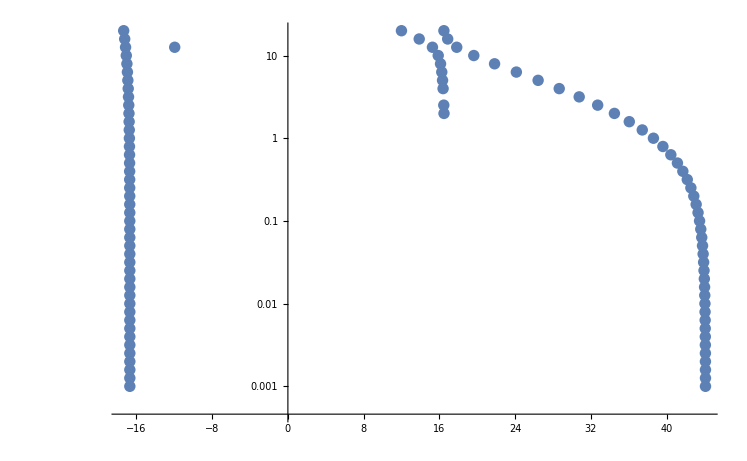

{{-44.0985,-0.001},{16.6916,-0.001},{-44.0969,-0.00125893},{16.6916,-0.00125893},{-44.0948,-0.00158489},{16.6916,-0.00158489},{-44.0921,-0.00199526},{16.6916,-0.00199526},{-44.0888,-0.00251189},{16.6917,-0.00251189},{-44.0846,-0.00316228},{16.6917,-0.00316228},{-44.0794,-0.00398107},{16.6917,-0.00398107},{-44.0728,-0.00501187},{16.6918,-0.00501187},{-44.0645,-0.00630957},{16.6919,-0.00630957},{-44.054,-0.00794328},{16.6919,-0.00794328},{-44.0408,-0.01},{16.692,-0.01},{-44.0242,-0.0125893},{16.6922,-0.0125893},{-44.0034,-0.0158489},{16.6923,-0.0158489},{-43.9772,-0.0199526},{16.6925,-0.0199526},{-43.9443,-0.0251189},{16.6928,-0.0251189},{-43.9029,-0.0316228},{16.6931,-0.0316228},{-43.8509,-0.0398107},{16.6935,-0.0398107},{-43.7857,-0.0501187},{16.694,-0.0501187},{-43.7039,-0.0630957},{16.6946,-0.0630957},{-43.6014,-0.0794328},{16.6954,-0.0794328},{-43.4731,-0.1},{16.6965,-0.1},{-43.3129,-0.125893},{16.6977,-0.125893},{-43.1132,-0.158489},{16.6993,-0.158489},{-42.8647,-0.199526},{16.7013,-0.199526},{-42.5566,-0.251189},{16.7038,-0.251189},{-42.1759,-0.316228},{16.7069,-0.316228},{-41.7077,-0.398107},{16.7108,-0.398107},{-41.1351,-0.501187},{16.7157,-0.501187},{-40.4395,-0.630957},{16.7218,-0.630957},{-39.6015,-0.794328},{16.7294,-0.794328},{-38.6017,-1.},{16.7389,-1.},{-37.4229,-1.25893},{16.7505,-1.25893},{-36.0515,-1.58489},{16.7649,-1.58489},{-16.4859,-1.99526},{-34.4808,-1.99526},{16.7826,-1.99526},{-16.462,-2.51189},{-32.7131,-2.51189},{16.8042,-2.51189},{-30.7619,-3.16228},{16.8305,-3.16228},{-16.3892,-3.98107},{-28.6529,-3.98107},{16.8623,-3.98107},{-16.3322,-5.01187},{-26.4243,-5.01187},{16.9005,-5.01187},{-16.2499,-6.30957},{-24.1262,-6.30957},{16.9463,-6.30957},{-16.1199,-7.94328},{-21.8252,-7.94328},{17.0009,-7.94328},{-15.8744,-10.},{-19.6315,-10.},{17.0656,-10.},{-15.2657,-12.5893},{-17.8301,-12.5893},{17.1423,-12.5893},{11.9524,-12.5893},{-13.8686,-15.8489},{-16.875,-15.8489},{17.2329,-15.8489},{-11.9927,-19.9526},{-16.4754,-19.9526},{17.3402,-19.9526}}

```mathematica
ListLogPlot[-taben,PlotRange->All]
taben
```

```mathematica
emin = -emin; emax = -emax;
```

```mathematica
rts1={};
Module[{pemin,pemax,pen,tabe,p},
tabe={};
dp=0.0008 emax;
p=emin;
While[p≤emax,AppendTo[tabe,p];p+=dp];
(*Print[tabe];*)
Print["Progress:"];
Print[ProgressIndicator[Dynamic[k],{1,Length[tabe]}]];
Do[en=tabe[[i]];
(*Print["en = ",en];*)
k=i;
bound=(x/.FindRoot[Sort[Eigenvalues[V[x]]][[1]]==en,{x,0.2, 1000}]);
xf = 5bound;
xmid = xi+ (bound-xi)/2;
nmid=1; 
While[xt[[nmid]]<xmid,nmid++];
nmid--;

(*Print["xi = ",xi, " xf = ",xf," xmid = ", xmid];*)


AppendTo[rts1, {tabe[[i]],RootsF[tabe[[i]],500]}]

,{i,1,Length[tabe]}
]
]
```

Progress:

Inverse::luc: Result for Inverse of badly conditioned matrix {{-1.20078×10^7,1.98088×10^7,-2.52512×10^7,-1.21257×10^7,-2.1352×10^6,-209851.,-13454.2,-612.793,-20.9481,-0.558739,«7»},{1.98089×10^7,-3.26779×10^7,4.16561×10^7,2.00033×10^7,3.52238×10^6,346185.,22194.9,1010.91,34.5575,0.921735,«7»},{-2.52519×10^7,4.1657×10^7,-5.31021×10^7,-2.54997×10^7,-4.49024×10^6,-441307.,-28293.5,-1288.68,-44.053,-1.175,«7»},{-1.21264×10^7,2.00044×10^7,-2.55006×10^7,-1.22454×10^7,-2.15629×10^6,-211924.,-13587.1,-618.846,-21.155,-0.564258,«7»},{«1»},{«1»},{«1»},{-612.979,1011.21,-1289.03,«6»,-0.00029988,«7»},{-20.9563,34.5708,-44.069,-21.162,-3.72643,-0.366302,-0.0241311,-0.0134586,0.963737,-0.00813648,«7»},{-0.559013,0.92218,-1.17555,-0.5645,-0.099403,-0.00977115,-0.000643574,-0.000299931,-0.00813701,1.03269,«7»},«7»} may contain significant numerical errors.

```mathematica
taben1={};tabphi1={};tabvec1={};
Do[AppendTo[taben1,{aHOz/ash[rts1[[n,2,1,m]]],1/Ωz rts1[[n,1]]}];AppendTo[tabphi1,{rts1[[n,2,1,m]],rts1[[n,1]]}];AppendTo[tabvec1,rts1[[n,2,2,m]]],{n,1,Length[rts1]},{m,1,Length[rts1[[n,2,1]]]}];
```

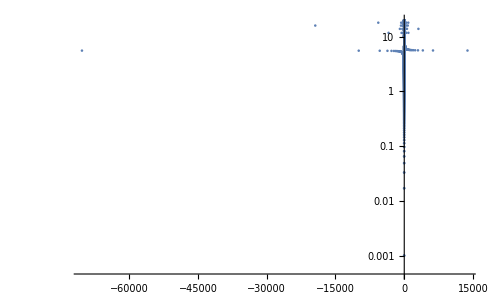

{{-44.0985,-0.001},{16.6916,-0.001},{-44.0969,-0.00125893},{16.6916,-0.00125893},{-44.0948,-0.00158489},{16.6916,-0.00158489},{-44.0921,-0.00199526},{16.6916,-0.00199526},{-44.0888,-0.00251189},{16.6917,-0.00251189},{-44.0846,-0.00316228},{16.6917,-0.00316228},{-44.0794,-0.00398107},{16.6917,-0.00398107},{-44.0728,-0.00501187},{16.6918,-0.00501187},{-44.0645,-0.00630957},{16.6919,-0.00630957},{-44.054,-0.00794328},{16.6919,-0.00794328},{-44.0408,-0.01},{16.692,-0.01},{-44.0242,-0.0125893},{16.6922,-0.0125893},{-44.0034,-0.0158489},{16.6923,-0.0158489},{-43.9772,-0.0199526},{16.6925,-0.0199526},{-43.9443,-0.0251189},{16.6928,-0.0251189},{-43.9029,-0.0316228},{16.6931,-0.0316228},{-43.8509,-0.0398107},{16.6935,-0.0398107},{-43.7857,-0.0501187},{16.694,-0.0501187},{-43.7039,-0.0630957},{16.6946,-0.0630957},{-43.6014,-0.0794328},{16.6954,-0.0794328},{-43.4731,-0.1},{16.6965,-0.1},{-43.3129,-0.125893},{16.6977,-0.125893},{-43.1132,-0.158489},{16.6993,-0.158489},{-42.8647,-0.199526},{16.7013,-0.199526},{-42.5566,-0.251189},{16.7038,-0.251189},{-42.1759,-0.316228},{16.7069,-0.316228},{-41.7077,-0.398107},{16.7108,-0.398107},{-41.1351,-0.501187},{16.7157,-0.501187},{-40.4395,-0.630957},{16.7218,-0.630957},{-39.6015,-0.794328},{16.7294,-0.794328},{-38.6017,-1.},{16.7389,-1.},{-37.4229,-1.25893},{16.7505,-1.25893},{-36.0515,-1.58489},{16.7649,-1.58489},{-16.4859,-1.99526},{-34.4808,-1.99526},{16.7826,-1.99526},{-16.462,-2.51189},{-32.7131,-2.51189},{16.8042,-2.51189},{-30.7619,-3.16228},{16.8305,-3.16228},{-16.3892,-3.98107},{-28.6529,-3.98107},{16.8623,-3.98107},{-16.3322,-5.01187},{-26.4243,-5.01187},{16.9005,-5.01187},{-16.2499,-6.30957},{-24.1262,-6.30957},{16.9463,-6.30957},{-16.1199,-7.94328},{-21.8252,-7.94328},{17.0009,-7.94328},{-15.8744,-10.},{-19.6315,-10.},{17.0656,-10.},{-15.2657,-12.5893},{-17.8301,-12.5893},{17.1423,-12.5893},{11.9524,-12.5893},{-13.8686,-15.8489},{-16.875,-15.8489},{17.2329,-15.8489},{-11.9927,-19.9526},{-16.4754,-19.9526},{17.3402,-19.9526}}

```mathematica
ListLogPlot[taben1,PlotRange->All]
taben
```

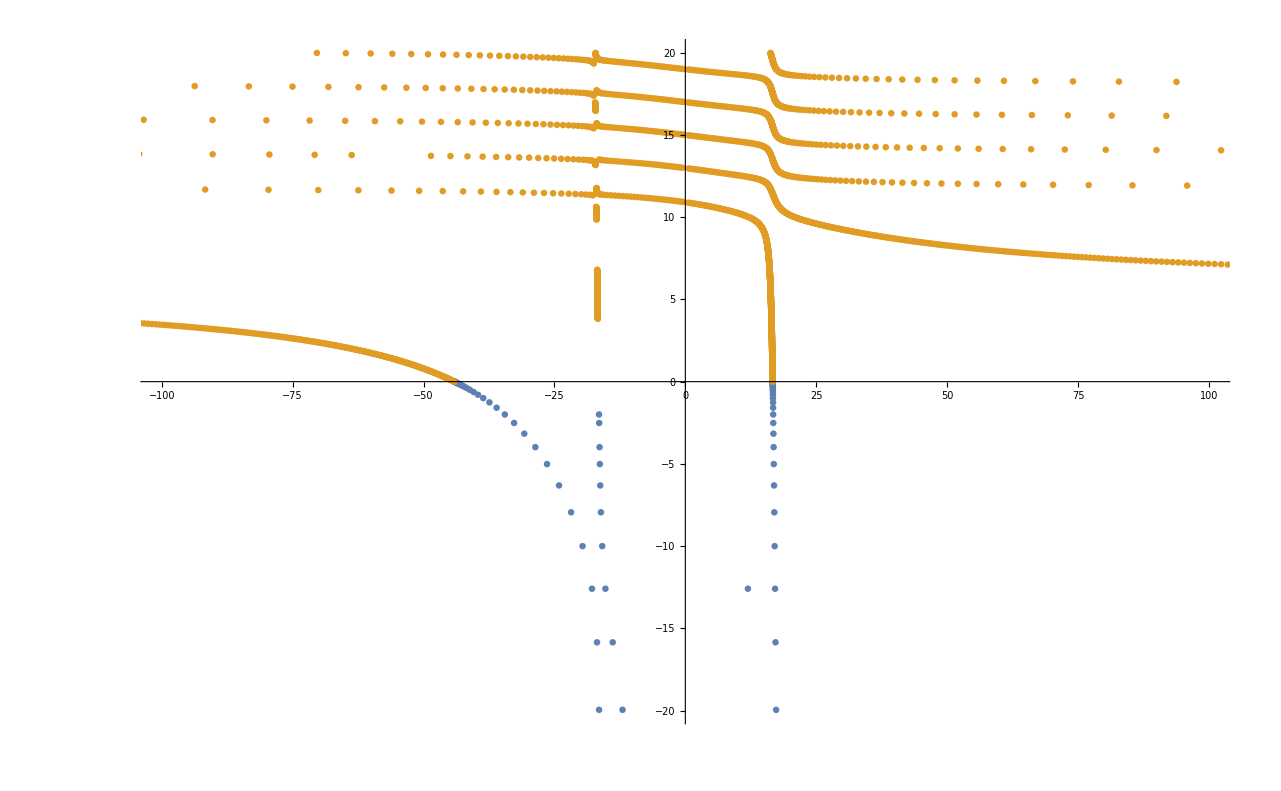

```mathematica
ListPlot[{taben,taben1},PlotRange->{{-100,100},{-20,20}}]
```

```mathematica
Export["Drop_3D_30_07.csv",Join[taben,taben1]]
```

Drop_3D_30_07.csv

```mathematica
tabb=Join[taben,taben1];
```

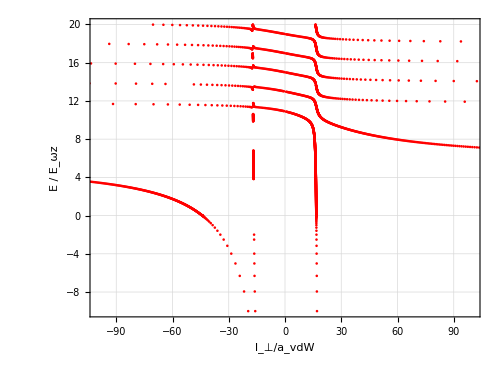

```mathematica
ListPlot[tabb,PlotRange->{{-100,100},{-10,20}},
AspectRatio->0.75,
Frame->True, FrameStyle->{{Directive[Thickness[0.005],Black],Directive[Thickness[0.005],Black]},{Directive[Thickness[0.005],Black],Directive[Thickness[0.005],Black]}},
PlotStyle->{Thick,{Red,Dashed}},FrameLabel->{Style["l_⊥/a_vdW",FontSize->20, FontFamily->"Times New Roman",FontWeight->Bold],Style["E / E_ωz",FontSize->20,FontWeight->Bold, FontFamily->"Times"]},GridLines->Automatic, GridLinesStyle->Directive[Thin, Dashed, LightGray],ImagePadding->50,ImageSize->500]
```

```mathematica
new=FindCurvePath[tabb.{{1,0},{0,100}}];
new1=Join[tabb[[#]]&/@new];
```

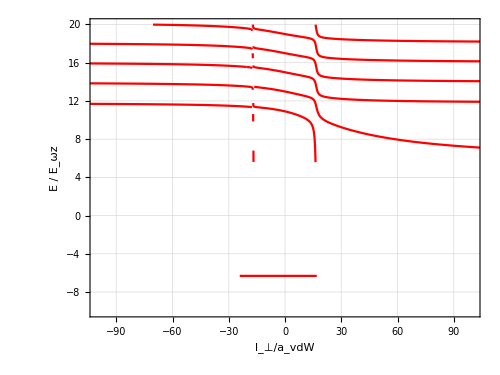

```mathematica
ListLinePlot[new1,PlotRange->{{-100,100},{-10,20}},
AspectRatio->0.75,
Frame->True, FrameStyle->{{Directive[Thickness[0.005],Black],Directive[Thickness[0.005],Black]},{Directive[Thickness[0.005],Black],Directive[Thickness[0.005],Black]}},
PlotStyle->Red,FrameLabel->{Style["l_⊥/a_vdW",FontSize->20, FontFamily->"Times New Roman",FontWeight->Bold],Style["E / E_ωz",FontSize->20,FontWeight->Bold, FontFamily->"Times"]},GridLines->Automatic, GridLinesStyle->Directive[Thin, Dashed, LightGray],ImagePadding->50,ImageSize->500]
```

```mathematica
tabela=Import["Drop_3D_30_07_2.csv"]
```

Import::nffil: File Drop_3D_30_07_2.csv not found during Import.

$Failed